```mathematica
(* Helper function for finding where points will be generated, based on the line and a split value ∈(0,1) *)
GetCoord[line_,split_]:=
{line[[1,1]]+split*(line[[2,1]]-line[[1,1]]),line[[1,2]]+split*(line[[2,2]]-line[[1,2]])};
(* Main recursive function. Returns a list of lines *)
SquareStacks[lineRoot_,depth_,alpha_] := Module[{i,lineList,splits,points,len},
splits=Sort[Table[RandomReal[],alpha]];
points=Table[GetCoord[lineRoot,splits[[i]]],{i,1,alpha}];
PrependTo[points,lineRoot[[1]]];
AppendTo[points,lineRoot[[2]]];
lineList={lineRoot};
For[i=1,i<=alpha+1,i++,
AppendTo[lineList,{points[[i]],{points[[i,1]]-(points[[i+1,2]]-points[[i,2]]),points[[i,2]]+points[[i+1,1]]-points[[i,1]]}}];
AppendTo[lineList,{points[[i+1]],{points[[i+1,1]]-(points[[i+1,2]]-points[[i,2]]),points[[i+1,2]]+points[[i+1,1]]-points[[i,1]]}}];
AppendTo[lineList,{{points[[i,1]]-(points[[i+1,2]]-points[[i,2]]),points[[i,2]]+points[[i+1,1]]-points[[i,1]]},{points[[i+1,1]]-(points[[i+1,2]]-points[[i,2]]),points[[i+1,2]]+points[[i+1,1]]-points[[i,1]]}}];
If[depth>1,
lineList=Join[lineList,SquareStacks[{{points[[i,1]]-(points[[i+1,2]]-points[[i,2]]),points[[i,2]]+points[[i+1,1]]-points[[i,1]]},{points[[i+1,1]]-(points[[i+1,2]]-points[[i,2]]),points[[i+1,2]]+points[[i+1,1]]-points[[i,1]]}},depth-1,alpha]];
]
];
Return[lineList];
];
(* Generates a square stack on a single line *)
PlotSquares[lineList_]:=Module[{gfxList},
gfxList=Table[Graphics[Line[lineList[[i]]]],{i,1,Length[lineList]}];
Show[gfxList]
];
(* Generates a set of lines based on input points, and generates a list of lines corresponding to square stacks on each
PlotSquares is still required for it to show *)
GenCenterShape[pointList_,depth_,alpha_]:=Module[{i,l},
l=Length[pointList];
Join[Table[SquareStacks[{pointList[[i]],pointList[[Mod[i,l]+1]]},depth,alpha],{i,1,l}]]
];
```

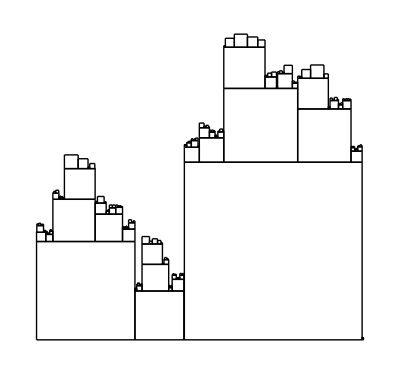

```mathematica
(* Example for a single line *)
PlotSquares[SquareStacks[{{0,0},{1,0}},4,4]]
```

```mathematica
(* Example for an octagon *)
PlotSquares[GenCenterShape[{{0,0},{0,3},{2,5},{5,5},{7,3},{7,0},{5,-2},{2,-2}},4,8]]
```

-Graphics-